# Tarea 2

Estudiante: José Alfredo de León Garrido

## Importe de paquete y rutinas nuevas

Asegúrese de haber clonado en su computadora el repositorio https://github.com/deleonja/mscsc_2022-2.git

De lo contrarrio, la siguiente línea no importará el paquete functions.wl

```mathematica
<<functions`
Import[StringJoin[Characters[NotebookFileName[]][[;;-12]]]<>"functions.wl"]
```

## Definición de rutinas

#### Polynomial Interpolation

```mathematica
(* Routine for polynomial interpolation of a data set {(Subscript[x, i],Subscript[y, i])} of n elements in a function f(x) =Subscript[a, 0]+Subscript[a, 1] x+…+Subscript[a, n-1] x^(n-1) *)
PolynomialInterpolation[x_,y_]:=Module[{X,AsSolutions,pos,Sol,n,AugM},
(* Compute the number of data points *)
n=Length[x];
(* Compute matrix of coefficients X *)
X=Table[If[#==0&&i==0,1,#^i],{i,0,n-1}]&/@x;
AugM=MapThread[Append,{X,y}];
(* Apply Gauss-Jordan elimination to the augmented matrix of the linear system for Subscript[a, i] *)
Sol=GaussJordan[AugM];
(* Sort the solutions Subscript[a, i] according to the column-swaps recorded in the second list of GaussJordan's output *)
GaussJordanSolution[Sol]
]

(* <<<<<<<<<<<<<<<<<<< miscelaneos>>>>>>>>>>>>>>>>>>>>>>*)


(* GaussJordanSolution[GJoutput] returns the ordered solution x⃗=(Subscript[x, 1],…,Subscript[x, N]) of a linear system of equations solved by GaussJordan routine. *)
Sorting[v_,w_]:=Part[v,Flatten[Position[w,#]&/@Range[Length[w]]]]
Clear[GaussJordanSolution]
GaussJordanSolution[GJoutput_]:=Module[{LastColOfRowReduced,newSolution,RowReduced,n,u},
LastColOfRowReduced=GJoutput[[1,All,-1]];
RowReduced=GJoutput[[1]];
n=Dimensions[RowReduced][[2]];
If[AnyTrue[u=(#≠1.&/@Round[Diagonal[RowReduced]]),TrueQ],
newSolution=ReplacePart[LastColOfRowReduced,#->0&/@Range[FromDigits[FirstPosition[u,True]],n]];
Sorting[newSolution,GJoutput[[2]]],
Sorting[LastColOfRowReduced,GJoutput[[2]]]
]
]
```

#### Splines

```mathematica
(* Función para generación de puntos con espaciamiento regular para el polinomio de interpolación *)
(* Para generar N puntos el intervalor [x1,x2] se debe dividir en N-1 *)
PuntosRegulares[x1_,x2_,n_]:=N[Range[x1,x2,(x2-x1)/(n-1)]]

(* Función para generar puntos con espaciamiento aleatorio *)
PuntosAleatorios[x1_,x2_,n_]:=N[Join[{x1},Sort[x1+Table[RandomReal[],n-2]*x2],{x2}]]

(* <<<<<<<<<< SPLINE INTERPOLATION >>>>>>>>>> *)

(* Linear spline *)
Spline[xi_,yi_,x_,1]:=Module[{α,β,f},
α=(RotateLeft[yi]-yi)/(RotateLeft[xi]-xi);(* Compute α *)
β=yi-xi α;(* compute β *)
β=β[[;;-2]];α=α[[;;-2]];(* drop last values of α and β *)
f=α x+β;(* load functions in an array *)
Piecewise[Table[{f[[i]],xi[[i]]≤x≤RotateLeft[xi][[i]]},{i,Length[xi]-1}]](* create the Mathematica function *)
]

(* Spline[xi,yi,x,3] computes the cubic spline interpolation of data set {xi,yi} and returns a funciton with the n-1 splines defined in the according intervals. xi, yi are 1-D arrays with the values of Subscript[x, j] and f(Subscript[x, j]). *)
Spline[xi_,yi_,x_,3]:=Module[{A,augmentedA,nonZeroAsIndices,a,b,c,d,h,XI,YI,CI,n,splineTerms},
(* Compute Subscript[x, j+1] in XI, Subscript[y, j+1] in YI, and n (number data points) *)
XI=RotateLeft[xi];YI=RotateLeft[yi];n=Length[xi];
(* Compute Subscript[h, j]=Subscript[x, j+1]-Subscript[x, j] *)
h=Part[XI-xi,1;;n];
(* Compute the {i,j}-> Subscript[A, i,j] for all Subscript[A, i,j]≠0 ....explicar más? *)
nonZeroAsIndices={{1,1}->1,{n,n}->1}~Join~Flatten[Table[{{i,i-1}->h[[i-1]],{i,i}->2(h[[i-1]]+h[[i]]),{i,i+1}->h[[i]]},{i,2,n-1}]];
(* Construct array with matrix A *)
A=SparseArray[nonZeroAsIndices,{n,n}];
(* Compute vector b⃗ *)
b=Join[{0},Table[FullSimplify[3/h[[i]](yi[[i+1]]-yi[[i]])-3/h[[i-1]](yi[[i]]-yi[[i-1]])],{i,2,n-1}],{0}];
(* Compute the augmented matrix of A c⃗=b⃗ *)
augmentedA=MapThread[Append,{Normal[A],b}];
(* Solve the linear equation A c⃗=b⃗ for c⃗. In this routine, we will use GaussJordan[M] *)
c=GaussJordanSolution[GaussJordan[augmentedA]];
(* Compute Subscript[c, j+1] in CI *)
CI=RotateLeft[c];
(* Compute the Subscript[b, j] coefficients *)
b=1/h(YI-yi)-h/3(2 c+CI);
(* Compute the Subscript[d, j] coefficients *)
d=1/(3h)(CI-c);
(* The last elements of every array with the coefficients of the splines must be dropped because there are only n-1 splines *)
{a,b,c,d}=Chop[{yi,b,c,d}[[All,;;-2]]]; 
(* Compute the terms (x-Subscript[x, i])^j of all splines *)
splineTerms=MapThread[Dot,{Table[(x-xi[[i]])^j,{i,n-1},{j,0,3}],Transpose[{a,b,c,d}]}];
(* Compute the piecewise function for the output of the routine, with every spline in its 
according interval *)
Piecewise[Table[{splineTerms[[i]],xi[[i]]≤x≤RotateLeft[xi][[i]]},{i,n-1}]]
]
```

## Parte 1

### i) f(x)=2cos(x)+sin(x)+√x, [0,2π]

#### 16 puntos

2.+4.12326 x-8.10506 x^2+12.4113 x^3-15.2805 x^4+13.3505 x^5-8.47424 x^6+4.00681 x^7-1.42619 x^8+0.38284 x^9-0.0770265 x^10+0.0114297 x^11-0.00121296 x^12+0.0000870498 x^13-3.78304×10^-6 x^14+7.51464×10^-8 x^15

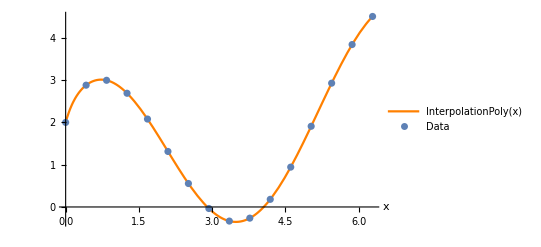

```mathematica
Clear[f];f[x_]:=N[2Cos[x]+Sin[x]+Sqrt[x]];
xi=PuntosRegulares[0,2π,16];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,15}]];IP[x]
fig=Show[Plot[IP[x],{x,0,2π},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

2.+5.1803 x-14.0626 x^2+26.4606 x^3-34.2401 x^4+29.9851 x^5-18.6135 x^6+8.46311 x^7-2.86699 x^8+0.728162 x^9-0.138187 x^10+0.0193157 x^11-0.00193077 x^12+0.000130608 x^13-5.35692×10^-6 x^14+1.00592×10^-7 x^15

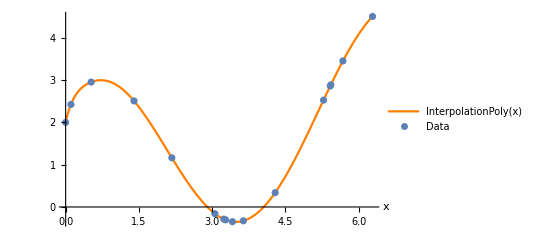

```mathematica
SeedRandom[22651]
Clear[f];f[x_]:=N[2Cos[x]+Sin[x]+Sqrt[x]];
xi=PuntosAleatorios[0,2π,16];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,15}]];IP[x]
fig=Show[Plot[IP[x],{x,0,2π},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

#### 32 puntos

2.+6.23465 x-35.4044 x^2+181.38 x^3-680.412 x^4+1869.68 x^5-3887.6 x^6+6269.52 x^7-7984.01 x^8+8129.95 x^9-6672.11 x^10+4428.6 x^11-2374.63 x^12+1021.74 x^13-347.934 x^14+91.6989 x^15-18.2735 x^16+2.90205 x^17-0.561103 x^18+0.186956 x^19-0.059304 x^20+0.01192 x^21-0.00074562 x^22-0.000373365 x^23+0.000151496 x^24-0.0000317708 x^25+4.50177×10^-6 x^26-4.54313×10^-7 x^27+3.252×10^-8 x^28-1.58039×10^-9 x^29+4.69751×10^-11 x^30-6.46571×10^-13 x^31

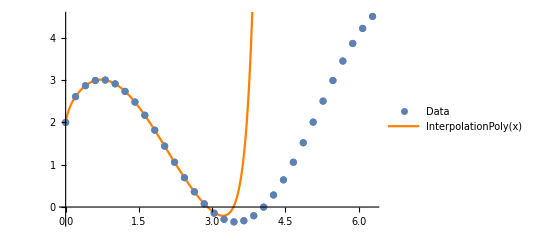

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+Sqrt[x];n=32;
xi=PuntosRegulares[0,2π,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
points=ListPlot[Transpose[Append[{xi},yi]]];
fig=Show[ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}],Plot[IP[x],{x,0,2π},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],points]
```

2.+4.95629 x-15.5905 x^2+42.7122 x^3-89.4637 x^4+137.381 x^5-159.758 x^6+144.318 x^7-103.436 x^8+60.1985 x^9-29.3353 x^10+12.4031 x^11-4.61194 x^12+1.40806 x^13-0.254305 x^14-0.0472621 x^15+0.0623384 x^16-0.0277011 x^17+0.0071763 x^18-0.000845542 x^19-0.000153048 x^20+0.000101171 x^21-0.0000256563 x^22+3.80466×10^-6 x^23-2.64465×10^-7 x^24-2.12425×10^-8 x^25+8.45005×10^-9 x^26-1.19176×10^-9 x^27+1.02045×10^-10 x^28-5.55991×10^-12 x^29+1.79079×10^-13 x^30-2.61708×10^-15 x^31

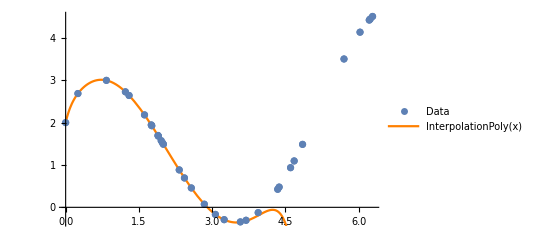

```mathematica
Clear[f];f[x_]:=N[2Cos[x]+Sin[x]+Sqrt[x]];n=32;
SeedRandom[43245]
xi=PuntosAleatorios[0,2π,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
points=ListPlot[Transpose[Append[{xi},yi]]];
fig=Show[ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}],Plot[IP[x],{x,0,2π},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],points]
```

#### 64 puntos

3.41421+1. x-1. x^2-0.166667 x^3+0.0833363 x^4+0.00831414 x^5-0.00268764 x^6-0.000516845 x^7+0.000919972 x^8-0.00187364 x^9+0.00323062 x^10-0.00447596 x^11+0.00499393 x^12-0.00445764 x^13+0.00311473 x^14-0.00160273 x^15+0.000480926 x^16+0.000071606 x^17-0.000200813 x^18+0.000144421 x^19-0.0000643839 x^20+0.0000176805 x^21-1.44823×10^-6 x^22-1.08304×10^-6 x^23+5.11192×10^-7 x^24-1.0517×10^-7 x^25+2.8947×10^-8 x^26-2.23739×10^-8 x^27+1.1175×10^-8 x^28-2.67609×10^-9 x^29+1.33741×10^-10 x^30+3.81295×10^-11 x^31+2.63893×10^-11 x^32-1.6271×10^-11 x^33+1.56383×10^-12 x^34+1.17547×10^-12 x^35-5.03045×10^-13 x^36+7.30586×10^-14 x^37+1.05242×10^-14 x^38-7.43772×10^-15 x^39+1.18257×10^-15 x^40+1.84599×10^-16 x^41-8.65955×10^-17 x^42-4.35263×10^-18 x^43+7.52745×10^-18 x^44-1.4267×10^-18 x^45+3.22711×10^-20 x^46+8.38345×10^-21 x^47+3.67878×10^-21 x^48-6.3787×10^-22 x^49-1.07507×10^-22 x^50+1.00299×10^-23 x^51+8.37848×10^-24 x^52-1.60164×10^-24 x^53-8.7027×10^-27 x^54+1.1395×10^-26 x^55+5.12646×10^-27 x^56-1.19706×10^-27 x^57-4.82119×10^-30 x^58+3.17601×10^-29 x^59-5.09772×10^-30 x^60+3.97005×10^-31 x^61-1.62146×10^-32 x^62+2.79934×10^-34 x^63

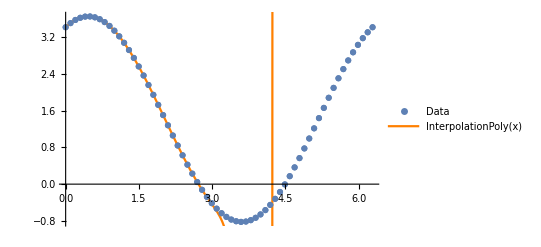

```mathematica
f[x_]:=N[2Cos[x]+Sin[x]+Sqrt[2]];n=64;
xi=PuntosRegulares[0,2π,n];yi=f[#]&/@xi;
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
points=ListPlot[Transpose[Append[{xi},yi]]];
fig=Show[ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}],Plot[IP[x],{x,0,2π},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],points]
```

3.41421+1. x-1. x^2-0.166643 x^3+0.0830903 x^4+0.00999598 x^5-0.0108649 x^6+0.0291059 x^7-0.0813639 x^8+0.176442 x^9-0.300821 x^10+0.403492 x^11-0.421209 x^12+0.332124 x^13-0.182561 x^14+0.0502199 x^15+0.0184742 x^16-0.0305152 x^17+0.0180372 x^18-0.00476762 x^19-0.00196253 x^20+0.00320155 x^21-0.00180502 x^22+0.000226661 x^23+0.000408359 x^24-0.000314009 x^25+0.0000920305 x^26-2.59655×10^-6 x^27-4.70617×10^-7 x^28-5.57571×10^-6 x^29+3.86774×10^-6 x^30-1.15864×10^-6 x^31+2.02893×10^-7 x^32-5.57379×10^-8 x^33+2.16946×10^-8 x^34-2.69757×10^-9 x^35-5.91147×10^-10 x^36-1.15135×10^-10 x^37+1.29047×10^-10 x^38+2.01091×10^-11 x^39-2.59557×10^-11 x^40+4.59579×10^-12 x^41+4.10137×10^-13 x^42-3.1902×10^-15 x^43-1.23773×10^-13 x^44+3.52109×10^-14 x^45-2.24944×10^-15 x^46-3.31134×10^-16 x^47-5.60971×10^-18 x^48+1.66868×10^-18 x^49+7.82111×10^-18 x^50-2.16856×10^-18 x^51+1.1223×10^-19 x^52+4.09115×10^-20 x^53-1.08753×10^-20 x^54+2.33443×10^-21 x^55-5.20847×10^-22 x^56+7.56391×10^-23 x^57-3.65904×10^-24 x^58-6.75715×10^-25 x^59+1.43043×10^-25 x^60-1.21829×10^-26 x^61+5.2612×10^-28 x^62-9.49401×10^-30 x^63

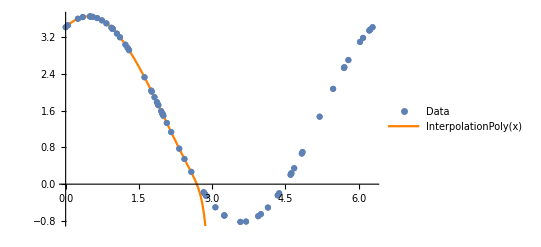

```mathematica
f[x_]:=N[2Cos[x]+Sin[x]+Sqrt[2]];n=64;
SeedRandom[43245]
xi=PuntosAleatorios[0,2π,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
points=ListPlot[Transpose[Append[{xi},yi]]];
fig=Show[ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}],Plot[IP[x],{x,0,2π},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],points]
```

### ii) f(x)=2cos(2π x)+sin(2π x)+√(2π x), [0,1]

#### 16 puntos

2.+25.9072 x-319.975 x^2+3078.63 x^3-23815.4 x^4+130736. x^5-521411. x^6+1.54902×10^6 x^7-3.46431×10^6 x^8+5.843×10^6 x^9-7.38649×10^6 x^10+6.88671×10^6 x^11-4.59203×10^6 x^12+2.07065×10^6 x^13-565403. x^14+70567.6 x^15

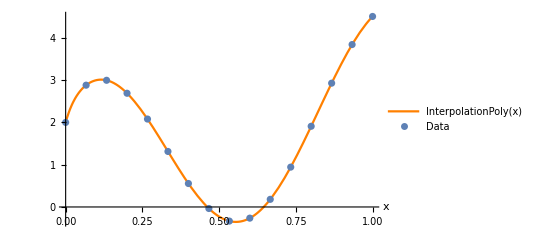

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+Sqrt[2π x];
xi=PuntosRegulares[0,1,16];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,15}]];IP[x]
fig=Show[Plot[IP[x],{x,0,1},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

2.+32.5488 x-555.167 x^2+6563.46 x^3-53363.6 x^4+293624. x^5-1.14522×10^6 x^6+3.27165×10^6 x^7-6.96366×10^6 x^8+1.11126×10^7 x^9-1.32503×10^7 x^10+1.16371×10^7 x^11-7.3087×10^6 x^12+3.10638×10^6 x^13-800520. x^14+94448.4 x^15

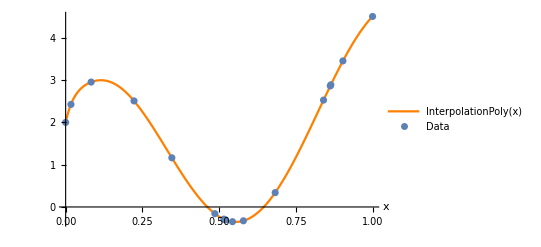

```mathematica
SeedRandom[22651]
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+Sqrt[2π x];
x0=0;xf=1;n=16;
xi=PuntosAleatorios[x0,xf,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
fig=Show[Plot[IP[x],{x,x0,xf},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

#### 32 puntos

2.+34.9638 x-922.007 x^2+21332.7 x^3-361709. x^4+4.42099×10^6 x^5-4.01947×10^7 x^6+2.77938×10^8 x^7-1.48197×10^9 x^8+6.13298×10^9 x^9-1.96817×10^10 x^10+4.85021×10^10 x^11-8.97827×10^10 x^12+1.20019×10^11 x^13-1.1034×10^11 x^14+7.92517×10^10 x^15-1.05539×10^11 x^16+2.1009×10^11 x^17-2.44233×10^11 x^18+7.18762×10^10 x^19+1.17353×10^11 x^20+1.51724×10^10 x^21-3.74969×10^11 x^22+4.66461×10^11 x^23-1.65187×10^11 x^24-7.32802×10^10 x^25-4.55163×10^10 x^26+2.65409×10^11 x^27-2.84859×10^11 x^28+1.51906×10^11 x^29-4.25988×10^10 x^30+5.05214×10^9 x^31

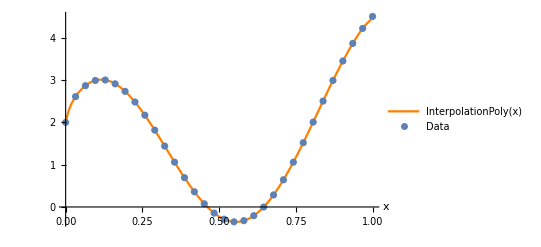

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+Sqrt[2π x];
x0=0;xf=1;n=32;
xi=PuntosRegulares[x0,xf,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
fig=Show[Plot[IP[x],{x,x0,xf},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

2.00004+41.556 x-1605.07 x^2+51199.5 x^3-1.08688×10^6 x^4+1.50825×10^7 x^5-1.33259×10^8 x^6+6.20518×10^8 x^7+8.96228×10^8 x^8-3.96607×10^10 x^9+3.46253×10^11 x^10-1.85636×10^12 x^11+6.96695×10^12 x^12-1.88229×10^13 x^13+3.57358×10^13 x^14-4.22796×10^13 x^15+1.31161×10^13 x^16+5.41832×10^13 x^17-1.06418×10^14 x^18+7.15338×10^13 x^19+4.43954×10^13 x^20-1.40326×10^14 x^21+1.43973×10^14 x^22-9.58815×10^13 x^23+5.73389×10^13 x^24-1.61544×10^13 x^25-4.81729×10^13 x^26+9.46742×10^13 x^27-8.47206×10^13 x^28+4.29424×10^13 x^29-1.19771×10^13 x^30+1.44116×10^12 x^31

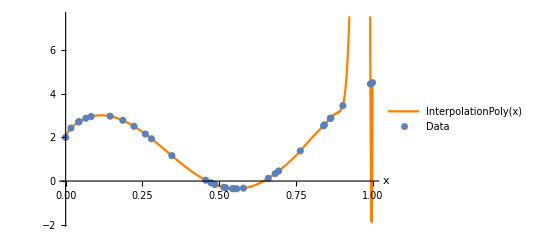

```mathematica
SeedRandom[22651]
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+Sqrt[2π x];
x0=0;xf=1;n=32;
xi=PuntosAleatorios[x0,xf,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
fig=Show[Plot[IP[x],{x,x0,xf},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

#### 64 puntos

2.00008+43.8098 x-1948.14 x^2+73163.9 x^3-1.89047×10^6 x^4+3.4139×10^7 x^5-4.47019×10^8 x^6+4.36491×10^9 x^7-3.24423×10^10 x^8+1.86207×10^11 x^9-8.32878×10^11 x^10+2.91473×10^12 x^11-7.96624×10^12 x^12+1.68336×10^13 x^13-2.68077×10^13 x^14+3.01005×10^13 x^15-1.85588×10^13 x^16-6.37658×10^12 x^17+2.90313×10^13 x^18-2.94806×10^13 x^19+3.38573×10^12 x^20+2.74701×10^13 x^21-3.25802×10^13 x^22+5.46508×10^12 x^23+2.79869×10^13 x^24-3.44508×10^13 x^25+1.13236×10^13 x^26-3.08372×10^12 x^27+3.05947×10^13 x^28-3.54686×10^13 x^29+1.38973×10^13 x^30-4.78272×10^13 x^31+8.38177×10^13 x^32-3.66604×10^13 x^33+2.8287×10^13 x^34-9.0739×10^13 x^35+6.62143×10^13 x^36+1.94583×10^13 x^37-5.73492×10^13 x^38+5.92227×10^13 x^39-2.20331×10^13 x^40-1.30318×10^13 x^41+1.49251×10^13 x^42-5.44873×10^13 x^43+6.00138×10^13 x^44+2.30164×10^13 x^45-4.75862×10^13 x^46+2.98584×10^13 x^47-3.1246×10^13 x^48-5.62397×10^13 x^49+1.13234×10^14 x^50-1.59728×10^13 x^51-6.26221×10^12 x^52-5.44793×10^13 x^53+8.13551×10^12 x^54+1.44787×10^13 x^55+3.90984×10^13 x^56-1.88958×10^13 x^57-3.35387×10^12 x^58-3.95238×10^13 x^59+3.88783×10^13 x^60+4.08051×10^12 x^61-1.47008×10^13 x^62+4.11395×10^12 x^63

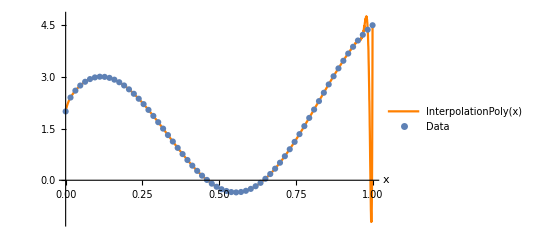

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+Sqrt[2π x];
x0=0;xf=1;n=64;
xi=PuntosRegulares[x0,xf,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
fig=Show[Plot[IP[x],{x,x0,xf},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

2.00002+43.5095 x-1930.41 x^2+73677.4 x^3-1.96361×10^6 x^4+3.70215×10^7 x^5-5.11064×10^8 x^6+5.29816×10^9 x^7-4.19633×10^10 x^8+2.56506×10^11 x^9-1.21397×10^12 x^10+4.42762×10^12 x^11-1.22498×10^13 x^12+2.48039×10^13 x^13-3.37675×10^13 x^14+2.31341×10^13 x^15+9.26529×10^12 x^16-3.01738×10^13 x^17+6.18183×10^12 x^18+2.75084×10^13 x^19-6.53633×10^12 x^20-3.52906×10^13 x^21+1.70125×10^13 x^22+1.53979×10^13 x^23+1.09836×10^13 x^24-2.2851×10^13 x^25-1.80047×10^13 x^26+3.75314×10^13 x^27-5.74367×10^13 x^28+7.2332×10^13 x^29+1.03603×10^13 x^30-6.70133×10^13 x^31-1.92609×10^12 x^32+3.22105×10^13 x^33-1.67797×10^13 x^34+1.06959×10^13 x^35+5.32412×10^13 x^36-4.39831×10^13 x^37-3.37792×10^13 x^38-9.89839×10^12 x^39+1.27834×10^13 x^40+6.65928×10^13 x^41-2.89273×10^13 x^42-7.12683×10^12 x^43-2.52163×10^12 x^44-4.18948×10^13 x^45+3.46944×10^13 x^46+1.00087×10^13 x^47-1.02641×10^13 x^48+2.67816×10^12 x^49+1.00731×10^13 x^50+8.40372×10^11 x^51-1.30292×10^13 x^52+4.98192×10^11 x^53-4.07129×10^13 x^54+4.6796×10^13 x^55+3.94481×10^13 x^56-4.04548×10^13 x^57-3.78195×10^13 x^58+3.79173×10^13 x^59+5.08789×10^12 x^60-1.07762×10^13 x^61+1.13787×10^12 x^62+5.69386×10^11 x^63

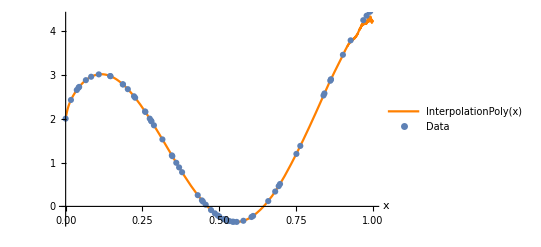

```mathematica
SeedRandom[22651]
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+Sqrt[2π x];
x0=0;xf=1;n=64;
xi=PuntosAleatorios[x0,xf,n];yi=f[xi];
A=PolynomialInterpolation[xi,yi];
IP[t_]:=Total[Table[A[[i+1]] t^i,{i,0,n-1}]];IP[x]
fig=Show[Plot[IP[x],{x,x0,xf},AxesLabel->Automatic,PlotLegends->{"InterpolationPoly(x)"},PlotStyle->{Orange}],ListPlot[Transpose[Append[{xi},yi]],PlotLegends->{"Data"}]]
```

## Parte 2

## f(x)=2cos(x)+sin(x)+√x

### 16 puntos

#### Spline lineal, espaciamiento regular

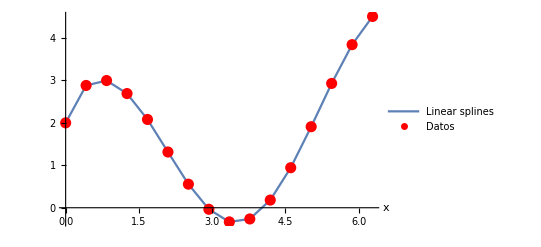

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=16;
xi=PuntosRegulares[0,2π,16];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,1],{x,0,2π},PlotLegends->{"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
```

#### Spline lineal, espaciamiento aleatorio

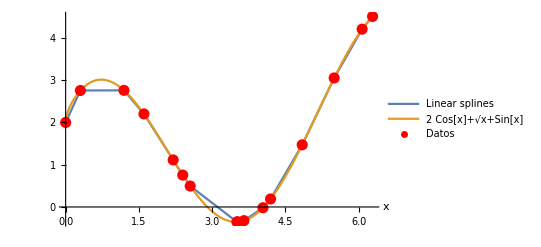

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=16;
SeedRandom[41234];
xi=PuntosAleatorios[0,2π,16];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{Spline[xi,yi,x,1],f[x]},{x,0,2π},PlotLegends->{"Linear splines",f[x]},AxesLabel->Automatic];
fig=Show[lines,points]
```

#### Spline cúbico, espaciamiento regular

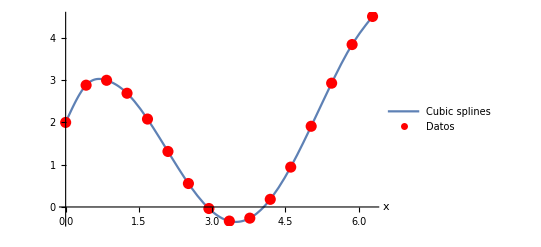

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=16;
xi=PuntosRegulares[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,3],{x,0,2π},PlotLegends->{"Cubic splines"},AxesLabel->Automatic];
fig=Show[lines,points]
```

#### Spline cúbico, espaciamiento aleatorio

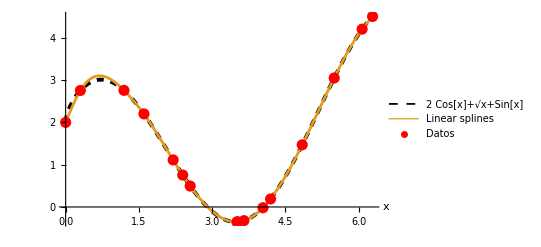

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=16;
SeedRandom[41234];
xi=PuntosAleatorios[0,2π,16];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{f[x],Spline[xi,yi,x,3]},{x,0,2π},PlotStyle->{{Black,Dashed,Thickness[0.007]},Thickness[0.005]},PlotLegends->{f[x],"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
```

### 32 puntos

#### Spline lineal, espaciamiento regular

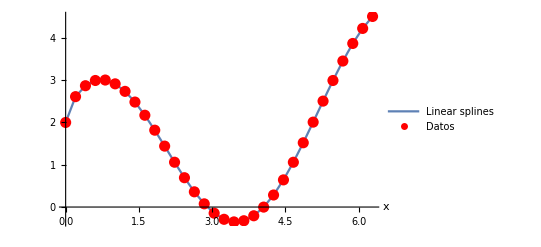

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=32;
xi=PuntosRegulares[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,1],{x,0,2π},PlotLegends->{"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
```

#### Spline lineal, espaciamiento aleatorio

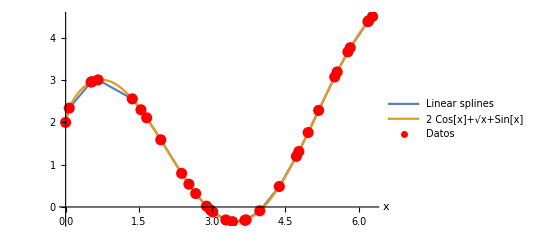

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=32;
SeedRandom[1234];
xi=PuntosAleatorios[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{Spline[xi,yi,x,1],f[x]},{x,0,2π},PlotLegends->{"Linear splines",f[x]},AxesLabel->Automatic];
fig=Show[lines,points]
```

#### Spline cúbico, espaciamiento regular

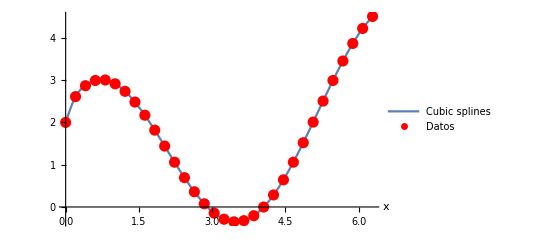

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=32;
xi=PuntosRegulares[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,3],{x,0,2π},PlotLegends->{"Cubic splines"},AxesLabel->Automatic];
fig=Show[lines,points]
```

#### Spline cúbico, espaciamiento aleatorio

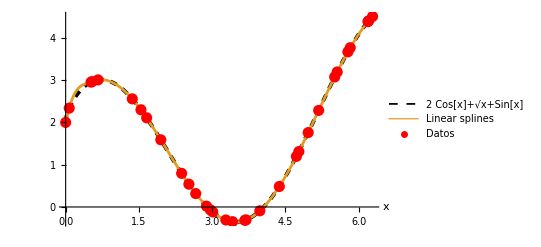

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=32;
SeedRandom[1234];
xi=PuntosAleatorios[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{f[x],Spline[xi,yi,x,3]},{x,0,2π},PlotStyle->{{Black,Dashed,Thickness[0.007]},Thickness[0.005]},PlotLegends->{f[x],"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
```

### 64 puntos

#### Spline lineal, espaciamiento regular

0.000304

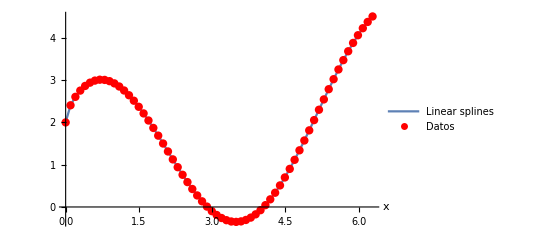

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=64;
xi=PuntosRegulares[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.015]}];
AbsoluteTiming[Spline[xi,yi,x,1]][[1]]
lines=Plot[Spline[xi,yi,x,1],{x,0,2π},PlotLegends->{"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline lineal, espaciamiento aleatorio

0.000227

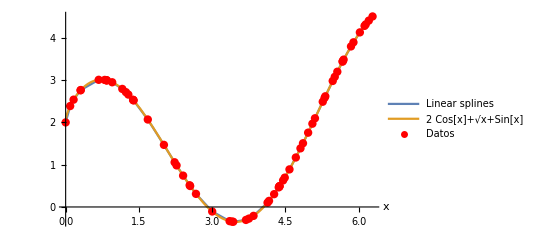

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=64;
SeedRandom[43524];
xi=PuntosAleatorios[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.015]}];
AbsoluteTiming[Spline[xi,yi,x,1]][[1]]
lines=Plot[{Spline[xi,yi,x,1],f[x]},{x,0,2π},PlotLegends->{"Linear splines",f[x]},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento regular

0.121878

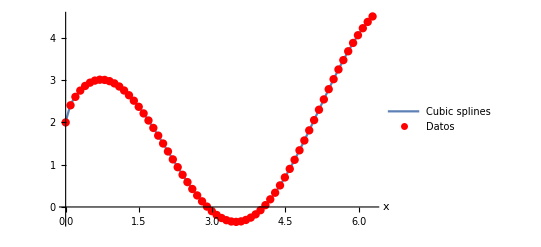

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=64;
xi=PuntosRegulares[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.015]}];
AbsoluteTiming[Spline[xi,yi,x,3]][[1]]
lines=Plot[Spline[xi,yi,x,3],{x,0,2π},PlotLegends->{"Cubic splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento aleatorio

0.111397

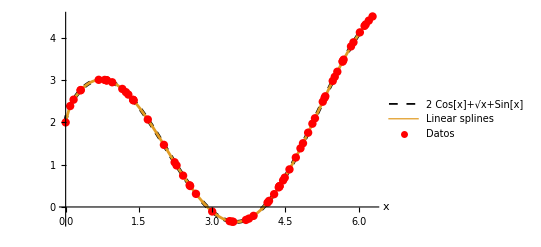

```mathematica
Clear[f];f[x_]:=2Cos[x]+Sin[x]+√x;n=64;
SeedRandom[43524];
xi=PuntosAleatorios[0,2π,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.015]}];
AbsoluteTiming[Spline[xi,yi,x,3]][[1]]
lines=Plot[{f[x],Spline[xi,yi,x,3]},{x,0,2π},PlotStyle->{{Black,Dashed,Thickness[0.007]},Thickness[0.005]},PlotLegends->{f[x],"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

## f(x)=2cos(2π x)+sin(2π x)+√(2π x)

### 16 puntos

#### Spline lineal, espaciamiento regular

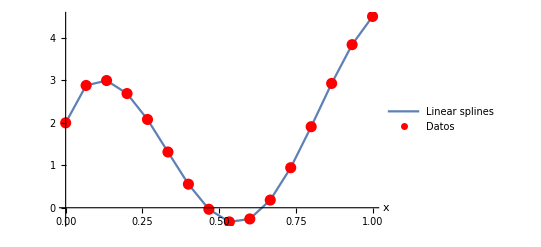

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=16;
xi=PuntosRegulares[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,1],{x,0,1},PlotLegends->{"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline lineal, espaciamiento aleatorio

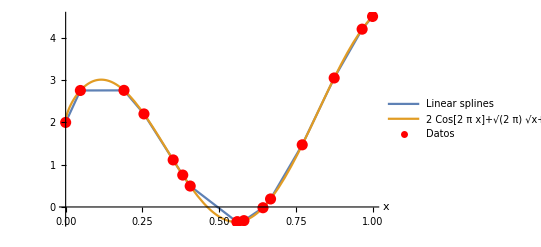

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=16;
SeedRandom[41234];
xi=PuntosAleatorios[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{Spline[xi,yi,x,1],f[x]},{x,0,1},PlotLegends->{"Linear splines",f[x]},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento regular

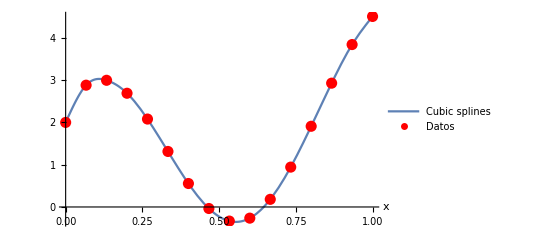

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=16;
xi=PuntosRegulares[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,3],{x,0,1},PlotLegends->{"Cubic splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento aleatorio

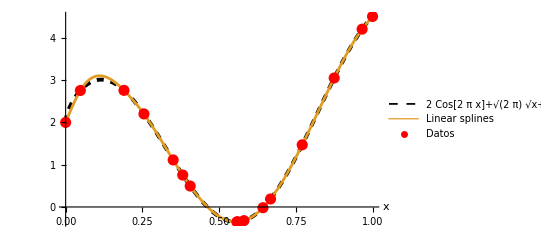

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=16;
SeedRandom[41234];
xi=PuntosAleatorios[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{f[x],Spline[xi,yi,x,3]},{x,0,1},PlotStyle->{{Black,Dashed,Thickness[0.007]},Thickness[0.005]},PlotLegends->{f[x],"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

### 32 puntos

#### Spline lineal, espaciamiento regular

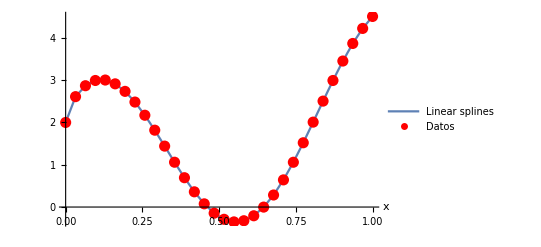

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=32;
xi=PuntosRegulares[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,1],{x,0,1},PlotLegends->{"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline lineal, espaciamiento aleatorio

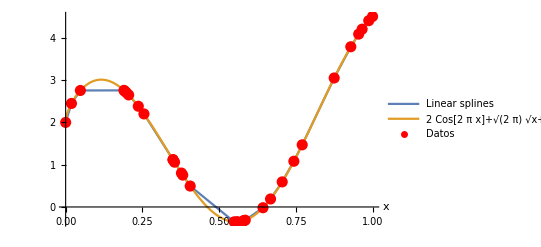

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=32;
SeedRandom[41234];
xi=PuntosAleatorios[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{Spline[xi,yi,x,1],f[x]},{x,0,1},PlotLegends->{"Linear splines",f[x]},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento regular

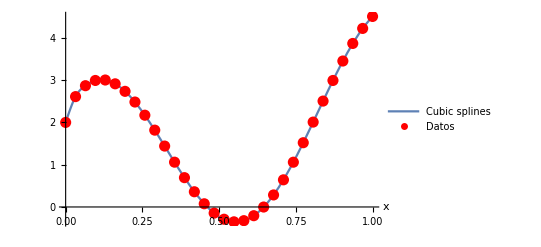

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=32;
xi=PuntosRegulares[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[Spline[xi,yi,x,3],{x,0,1},PlotLegends->{"Cubic splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento aleatorio

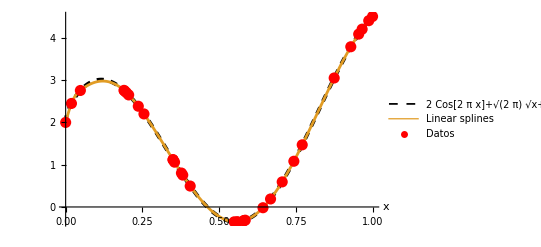

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=32;
SeedRandom[41234];
xi=PuntosAleatorios[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.02]}];
lines=Plot[{f[x],Spline[xi,yi,x,3]},{x,0,1},PlotStyle->{{Black,Dashed,Thickness[0.007]},Thickness[0.005]},PlotLegends->{f[x],"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

### 64 puntos

#### Spline lineal, espaciamiento regular

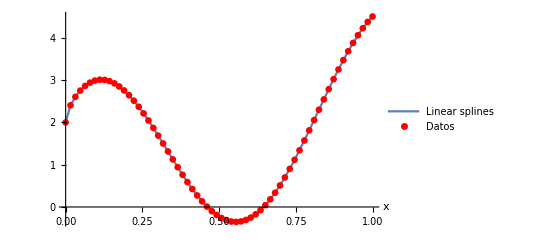

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=64;
xi=PuntosRegulares[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.012]}];
lines=Plot[Spline[xi,yi,x,1],{x,0,1},PlotLegends->{"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline lineal, espaciamiento aleatorio

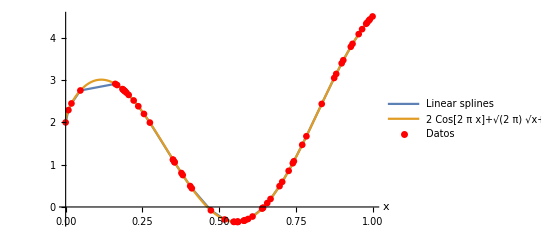

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=64;
SeedRandom[41234];
xi=PuntosAleatorios[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.012]}];
lines=Plot[{Spline[xi,yi,x,1],f[x]},{x,0,1},PlotLegends->{"Linear splines",f[x]},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento regular

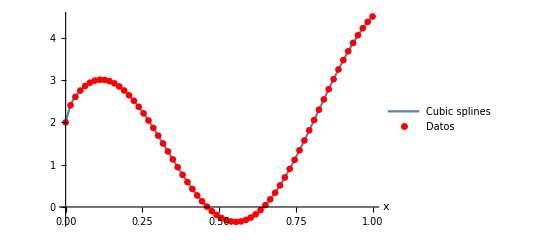

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=64;
xi=PuntosRegulares[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.012]}];
lines=Plot[Spline[xi,yi,x,3],{x,0,1},PlotLegends->{"Cubic splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```

#### Spline cúbico, espaciamiento aleatorio

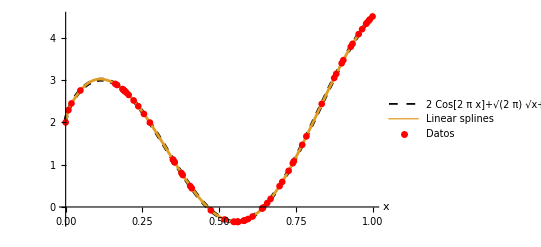

```mathematica
Clear[f];f[x_]:=2Cos[2π x]+Sin[2π x]+√(2π x);n=64;
SeedRandom[41234];
xi=PuntosAleatorios[0,1,n];yi=f[xi];
points=ListPlot[{#,f[#]}&/@xi,PlotLegends->{"Datos"},PlotStyle->{Red,PointSize[0.012]}];
lines=Plot[{f[x],Spline[xi,yi,x,3]},{x,0,1},PlotStyle->{{Black,Dashed,Thickness[0.007]},Thickness[0.005]},PlotLegends->{f[x],"Linear splines"},AxesLabel->Automatic];
fig=Show[lines,points]
AppendTo[figs,fig];
```